## Learning probability distributions

This chapter presents important techniques in statistics and machine learning which allow data to be described in terms of theoretical probability distributions or numerically build probability distributions from data. These tasks are called “find a distribution” and “learn a distribution” from data, respectively. Before covering these topics in the last two sections of the notebook, an revision of probability distributions is given in the first four sections of the notebook.

## Probability distributions revision (optional)

A revision on probability distributions is given in the next four sections. This is included as optional material that you can cover if you feel your knowledge about probability distributions is a bit rusty.

## Random variable

A random variable (r.v.) is a numerical description of the outcome of an experiment that involves randomness. 

Unlike normal variables such as the weight of a kilogram of potatoes, random variables do not take a fixed value.

Random variables are used extensively in sciences. Machine learning is not an exception.

There are two types of random variables: discrete and continuous.

Discrete r.v.: Can take a countable number of distinct values.

Examples: Number of children in a randomly selected family, number of e-mails received in one day, number of times we win the lottery.

Continuous r.v.: Can assume any value in some interval on the real number line.

Examples: Weight of a randomly picked orange in the supermarket, rainfall in one month, magnitude of an earthquake.

## Discrete r.v.

### Probability distribution

Let X be a discrete r.v. taking K discrete values {x_1,x_2,...,x_K}

Any value x_koccurs with probability P(X=x_k)=p_k

The probability distribution of X is the list of probabilities for all the possible values of X:

		{p_1,p_2,..., p_K}

Some probability distributions appear more frequently in applications than other. For the purposes of this course, we will mostly consider the following:

Bernoulli distribution

Binomial distribution

### Bernoulli distribution

Let us consider a random variable X the can only take two values.

In general, we refer to these two values as success (S) and failure (F).

Examples: Tossing a coin, winning/losing the lottery, win/lose a prize

Probability distribution: {p,q}

p: probability of success

q: probability of failure

This probability distribution plays an important role in the logistic regression method for classification.

### Example - A raffle

A bag contains 100 tickets of which only 10 contain a prize. 

Suppose 1000 people play the game. 
What is the probability p that someone will get a prize?
What is the probability q of getting no prize?

#### Answer

In this case, the answer is easy:

p=(Number of prizes)/(Number of tickets)=10/100=0.1

q=(Number of no prizes)/(Number of tickets)=90/100= 0.9

In general, q=1-p.  Therefore, the Bernoulli distribution is fully characterised by p, the probability of success.

A r.v. X obeying the Bernoulli distribution is denoted as

			X\[Distributed]Ber(p)

The symbol “\[Distributed]” can be read as “distributed as”. In Mathematica, it can be typed with the combination esc + dist + esc.

#### Simulation

One can also simulate this...

Define the bag:

```mathematica
bag=Flatten[{ConstantArray["prize",10],ConstantArray["no prize",100-10]}]
```

{prize,prize,prize,prize,prize,prize,prize,prize,prize,prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize,no prize}

Random variables are numerical descriptions of each outcome. We need to represent the results in the bag by numbers.

I replace “prize” by 1 and “no prize” by 0.

```mathematica
bagrv=ReplaceAll[{"prize"->1,"no prize"-> 0}][bag]
```

{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

1000 people playing corresponds to 1000 random choices from the bag:

```mathematica
RandomChoice[bagrv]
```

0

```mathematica
trials1000=RandomChoice[bagrv,1000];
```

The probability of success is then estimated by the fraction of people obtaining a prize:

```mathematica
p=Count[trials1000,1]/1000
```

109/1000

```mathematica
N[%]
```

0.109

It is indeed close to the expected probability, p = 0.1

An even closer value to 0.1 would be obtained if more people would play... Try for, e.g. 10000 people playing.

Plot of the distribution:

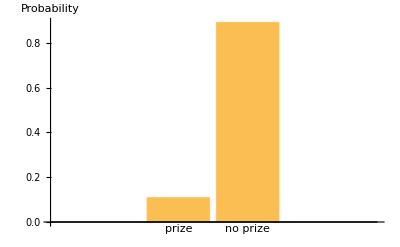

```mathematica
BarChart[{p,1-p},ChartLabels->{"prize","no prize"},AxesLabel->"Probability"]
```

### The Bernoulli distribution in Wolfram Language

BernoulliDistributionpaclet:ref/BernoulliDistribution[p]  represents a Bernoulli distribution with probability parameter p.

The probability distribution can be displayed for any p using the function PDF. Success and failure correspond to 0 and 1, respectively.

```mathematica
PDF[BernoulliDistribution[prob],k]
```

Piecewise[{{1-prob, k==0}, {prob, k==1}, {0, True}}]

Probability of success in the raffle game is

```mathematica
PDF[BernoulliDistribution[0.10],0]
```

0.9

and that of failure

```mathematica
PDF[BernoulliDistribution[0.10],0]
```

0.9

#### Bernoulli random variates

In the raffle example, we simulated the outcome of a random draw by sampling from the “bag” list. In general, if we know that the outcome follows a Bernoulli distribution, we can easily obtain random draws as random variates from the Bernoulli distribution.

In Mathematica, n random variates for a distribution dist are obtained with RandomVariatepaclet:ref/RandomVariate[dist,n].

For example, 10 draws in the raffle problem can be simulated as follows

```mathematica
trials10=RandomVariate[BernoulliDistribution[0.1],10]
```

{0,1,0,0,0,0,0,0,0,0}

Note that we don’t need the “bag” list once we have recognized that the outcome of the experiment can be described as a random variable X\[Distributed]Ber(0.1).

#### Expectation

What is the expected result in a number of experiments?

We normally take the mean.

In the raffle example, on average one gets 0.1 prizes every time we play:

```mathematica
N[Mean[trials1000]]
```

0.108

0.1 is not an integer number of prizes but we can interpret this as follows: On average, one has to play 10 times to get one prize.

In general, the expectation of a random variable X is denoted as E(X)

In Mathematica:

```mathematica
Expectation[x,x\[Distributed]BernoulliDistribution[p]]
```

p

If X~Ber(p) then E(X)=p.

```mathematica
Expectation[x,x\[Distributed]BernoulliDistribution[0.1]]
```

0.1

#### Dispersion

The dispersion of the values of a random variable is often measured in terms of the variance or standard deviation.

SD(X) = √(Var(X))

For the raffle game,

```mathematica
N[Variance[trials1000]]
```

0.0972162

```mathematica
%//Sqrt
```

0.311795

```mathematica
N[StandardDeviation[trials1000]]
```

0.311795

In Mathematica:

```mathematica
Variance[BernoulliDistribution[p]]
```

(1-p) p

```mathematica
Variance[BernoulliDistribution[0.1]]
```

0.09

```mathematica
StandardDeviation[BernoulliDistribution[p]]
```

√((1-p) p)

### Binomial distribution

The binomial distribution gives the probability that we get k successes in n Bernoulli trials.

This is an important distribution related to the Bernoulli distribution.

A r.v. X obeying the Binomial distribution with n attempts and probability of success p in each attempt is denoted as 

			X\[Distributed]Bin(n,p)

Remark: If we do a single attempt, i.e n=1, the binomial distribution reduces to the Bernoulli distribution.

More on the binomial distribution will be covered in more detail in PX5010 - Statistics and Times Series Analysis.

## Continuous r.v.

If X is a continuous r.v., we need the probability density function (p.d.f.) concept.

Example of continuous r.v.: Height of people, speed of molecules in a gas, etc

The problem with continuous random variables is that the values they take cannot be enumerated (they can take any value in an interval of the real numbers)

### Mission impossible - Hitting a real number

1000 random numbers in [0,1]

```mathematica
randset=RandomReal[{0,1},10000];
```

Number of times we get 0.5?

```mathematica
Count[randset,0.5]
```

0

You will most likely get 0... It is essentially impossible to land at random on any specific random real... Real numbers are a complicated set.

### Consider intervals

Idea: Consider the probability to fall in a certain interval, e.g. [0.45,0.5]

```mathematica
Count[randset,u_/;0.5≥u≥0.45]
```

494

### Histogram

You have already seen histograms in the course. 

Histograms represent the number of values of a continuous random variable in different bins (intervals defined by us or Wolfram Language)

For the set used above,

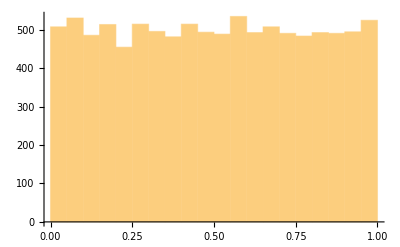

```mathematica
Histogram[randset]
```

### Probability density function

The probability density function (pdf) of a continuous r.v. X is a non-negative function, f, such that 
			P(x≤X≤x+Δx)=f(x)Δx

Normalization

Since the probability that the random variable takes any value in [-∞,+∞] must be P(Ω)=1 (i.e. the probability of the whole sample space),

P(-∞<X<∞) = Area under f(x) = 1

### Normal distribution

The normal distribution is the most ubiquitous of all distributions.

Any variation which is the sum of many small independent contributions, leads to normal r.v.’s

Examples:

Height of people (“height” depends on several factors - diet, genes, history of illness, etc)

Annual rainfall (several factors will affect the variations in annual rainfall)

The p.d.f. for the normal distribution is

```mathematica
PDF[NormalDistribution[μ,σ],x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

Here,

μ=E(X)  - Expectation

σ^2=Var(X)  - Variance

σ=SD(X) - Standard deviation

A random variable X obeying a normal distribution with mean μ and variance σ^2 is denoted as

							X\[Distributed]N(μ,σ^2)

#### Effect of varying μ

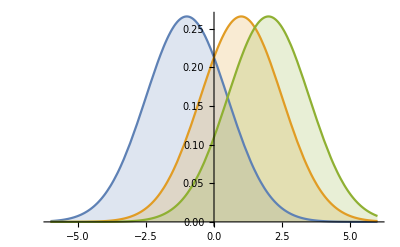

```mathematica
Plot[Table[PDF[NormalDistribution[μ,1.5],x],{μ,{-1,1,2}}]//Evaluate,{x,-6,6},Filling->Axis]
```

#### Effect of varying σ

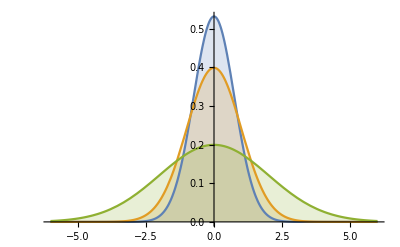

```mathematica
Plot[Table[PDF[NormalDistribution[0,σ],x],{σ,{.75,1,2}}]//Evaluate,{x,-6,6},Filling->Axis]
```

#### Normally distributed random numbers - Artificial data

One can use the RandomVariate function to generate normally distributed random numbers. 

In Section 3.2 on classification, we generated artificial data using random variates for the normal distribution. Specifically, we constructed training data set for two classes A and B simulated as two random variables  considered two random variables, X_A\[Distributed]N(-2,2^2) and X_B\[Distributed]N(2,2^2) :

```mathematica
n=50;  (*Number of random variates for each random variable*)
μ=2;
σ=2;
XA=RandomVariate[NormalDistribution[-μ,σ],n];
XB=RandomVariate[NormalDistribution[μ,σ],n];
```

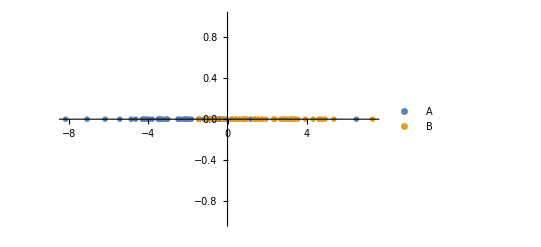

```mathematica
ListPlot[{Transpose[{XA,Table[0,{i,1,n}]}],Transpose[{XB,Table[0,{i,1,n}]}]},PlotMarkers->{"OpenMarkers", Medium},PlotLegends->{"A","B"}]
```

To illustrate the KNN method in Section 3.3, we generated data in which examples are characterised by two features. This was simulated with 2D data simulated as bi-variate random variables from a multinormal distribution as follows:

```mathematica
gaussian[μ_,σ_,n_]:=RandomVariate[MultinormalDistribution[μ,{{σ,0},{0,σ}}],n];
cluster1=gaussian[{3.5,2},0.3,500];
cluster2=gaussian[{2,3},0.5,30];
```

```mathematica
cluster1
```

{{3.10501,1.99119},{3.5951,2.19453},{3.55977,1.69716},{2.47732,2.43175},{3.22912,2.75029},{4.24109,1.54306},{3.12349,1.55801},{2.7515,2.27522},{3.06768,1.86261},{3.6613,1.91259},{4.32256,1.92479},{3.78256,0.723919},{3.60199,2.65438},{4.27289,1.71971},{2.87259,0.975329},{4.14766,1.79769},{4.33554,1.88532},{2.47928,2.77116},{4.5552,0.603131},{3.60173,2.14342},{3.13498,1.99689},{3.54635,1.32223},{3.23032,1.92824},{3.83001,2.3687},{3.97019,1.09328}}

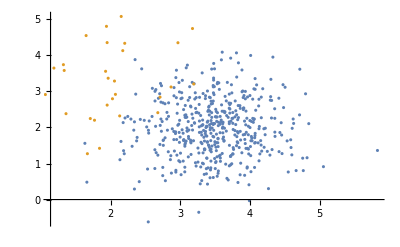

```mathematica
ListPlot[{cluster1,cluster2}]
```

Note that μ is a list with two elements, i.e. is the mean value of the bi-variate random variable.

#### Tasks for your

1. Consider a random variable Y=X_1+X_2+X_3, where X_1\[Distributed]N(1,4), X_2\[Distributed]N(-1,2), X_3\[Distributed]N(0,1).

Obtain 1000 random variates for Y.

Plot the values of  the random variates for Y in the axis of real numbers.

Calculate the mean and variance of the random variates. Can you explain the obtained values for the mean and variance in terms of the mean and variance of the random variables X_1, X_2 and X_3.

2. Consider a bi-variate random variable Z=(X_1,X_2).

Obtain 100 random variates for Z.

Do a scatterplot of the random variates of Z on the 2D plane.

Try to obtain 100 random variates for Z using the MultinormalDistribution. Plot these random variates together with those obtained in the previous item. Did you get a similar cloud of points with both procedures?

## Other distributions

In addition to Bernoulli, binomial and normal distributions there are many other distributions that are useful to describe certain random variables. The Wolfram Mathematica guide on Parametric Statistical Distributions provide many examples for distributions of random variables.

PX5010 - Statistics and Times Series Analysis will cover more on random variables and distributions.

## Finding and learning distributions from data

The next two sections are the core of this chapter. They are not optional and must be covered.

## Finding distribution of data - Classifying data into distributions

Given a set of random values, one can use the Wolfram Language function FindDistribution to find the distribution that best describes the data.

This can be viewed as a classification machine learning task: We input data to Mathematica and it is classified into a set of possible distributions (these are the categories).

### Example

For instance, the probability of 1000 values for X~Ber(0.2) can be found as follows:

```mathematica
data=RandomVariate[BernoulliDistribution[0.2],1000];
```

```mathematica
estimated𝒟=FindDistribution[data]   (* here, symbol 𝒟 can be typed as esc+scD+esc*)
```

BinomialDistribution[1,0.221854]

In fact, the binomial distribution for one attempt corresponds to Bernoulli distribution.

The estimated distribution is indeed close to the original distribution

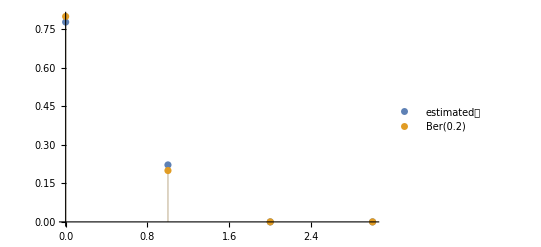

```mathematica
ListPlot[{Table[{k,PDF[estimated𝒟,k]},{k,0,3}],Table[{k,PDF[BernoulliDistribution[0.2],k]},{k,0,3}]},Filling->Axis,PlotLegends->{"estimated𝒟","Ber(0.2)"},PlotRange->All]
```

### Example

The BuffaloSnow dataset from the Wolfram Data Repository gives the snow accumulations in inches for Buffalo, New York from 1910 to 1972. We want to find the distribution of the snow accumulations.

The description of the data is

```mathematica
ExampleData[{"Statistics","BuffaloSnow"},"LongDescription"]
```

Snow accumulations in inches for Buffalo, New York from 1910 to 1972.

Other properties of the dataset:

```mathematica
ExampleData[{"Statistics","BuffaloSnow"},"Properties"]
```

{ApplicationAreas,ColumnDescriptions,ColumnHeadings,ColumnTypes,DataElements,DataType,Description,Dimensions,EventData,EventSeries,LongDescription,Name,ObservationCount,Source,TimeSeries}

We first download the data:

```mathematica
buffaloSnow=ExampleData[{"Statistics","BuffaloSnow"},"DataElements"]
```

{126.4,82.4,78.1,51.1,90.9,76.2,104.5,87.4,110.5,25,69.3,53.5,39.8,63.6,46.7,72.9,79.7,83.6,80.7,60.3,79,74.4,49.6,54.7,71.8,49.1,103.9,51.6,82.4,83.6,77.8,79.3,89.6,85.5,58,120.7,110.5,65.4,39.9,40.1,88.7,71.4,83,55.9,89.9,84.8,105.2,113.7,124.7,114.5,115.6,102.4,101.4,89.8,71.5,70.9,98.3,55.5,66.1,78.4,120.5,97,110}

It is always useful to explore the data a bit.

```mathematica
Take[buffaloSnow,10]
```

{126.4,82.4,78.1,51.1,90.9,76.2,104.5,87.4,110.5,25}

The snow accumulation is a continuous variable and a histogram gives an idea of what kind of distribution we expect for the snow accumulation.

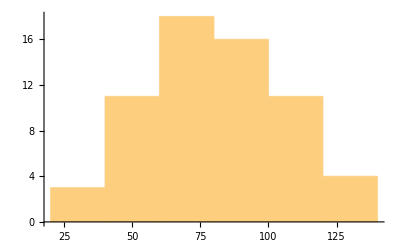

```mathematica
Histogram[buffaloSnow]
```

Wolfram finds the following distribution:

```mathematica
estDbuffalo=FindDistribution[buffaloSnow,3]
```

{NormalDistribution[80.1623,24.8373],MixtureDistribution[{0.404854,0.595146},{NormalDistribution[79.3529,14.9928],UniformDistribution[{25.052,126.475}]}],MixtureDistribution[{0.8613,0.1387},{NormalDistribution[74.3344,21.496],NormalDistribution[116.352,7.5904]}]}

One can compare the fitted distribution with the histogram of the data. Note that the histogram is normalized here to show an estimate of the probability density function (PDF) comparable in scale to the fitted pdf.

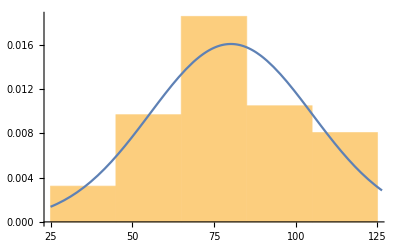

```mathematica
Show[{Histogram[buffaloSnow,{Min[buffaloSnow],Max[buffaloSnow],20},"PDF"],Plot[PDF[estDbuffalo[[1]],x],{x,Min[buffaloSnow],Max[buffaloSnow]}]}]
```

### Task for you

Repeat the steps in the previous example but now for the “ChickenWeight” dataset from the Wolfram Repository. Do you expect a normal distribution for the weight of chickens? Do you find enough evidence in favour of a normal distribution?

## Learning distributions

In the previous section, we have seen how to classify data into known, important distributions.

In some cases, it might not be possible to find a known distribution that fits well the data. In this case, it is possible to use a machine learning procedure that uses data to train an object that attempts to represent an underlying distribution for the examples given.

In Wolfram Language, this is achieved with the LearnDistribution function.

### Discrete random variables

```mathematica
data=RandomVariate[BinomialDistribution[5,0.2],100];
```

```mathematica
data
```

{1,1,0,1,1,3,0,1,1,2,0,0,3,2,1,2,2,1,2,2,1,0,1,3,2,1,1,2,1,2,1,0,1,0,0,1,1,1,2,1,0,1,1,2,0,2,2,1,0,1,0,2,2,0,2,1,1,0,1,2,0,2,1,0,1,0,3,0,1,1,2,2,1,0,1,0,1,0,2,2,0,0,1,1,1,2,0,1,2,1,1,0,2,2,2,0,2,2,0,2}

```mathematica
Tally[data]
```

{{1,39},{0,27},{3,4},{2,30}}

```mathematica
ld=LearnDistribution[data]
```

LearnedDistribution[…]

A new example based on the learned distribution:

```mathematica
Tally[RandomVariate[ld,1000]]
```

{{0,284},{1,362},{2,316},{3,38}}

```mathematica
RandomVariate[NormalDistribution[]]
```

```mathematica
PDF[NormalDistribution[]]
```

Function[x,(ⅇ^(-x^2/2))/(√(2 π))]

The probability distribution for any integer:

```mathematica
PDF[ld]
```

PDF[LearnedDistribution[…]]

```mathematica
PDF[ld,Range[6]]
```

{0.389994,0.299998,0.0400084,2.22507×10^-308,2.22507×10^-308,2.22507×10^-308}

The plot of the learned probability distribution:

General::munfl: 2.22507×10^-308 0.05 is too small to represent as a normalized machine number; precision may be lost.

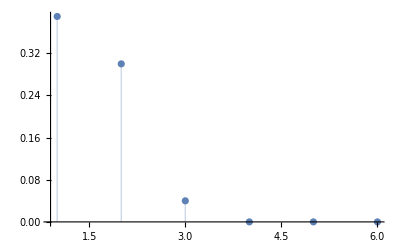

```mathematica
ListPlot[Transpose[{Range[6],PDF[ld,Range[6]]}],Filling->Axis,PlotRange->All]
```

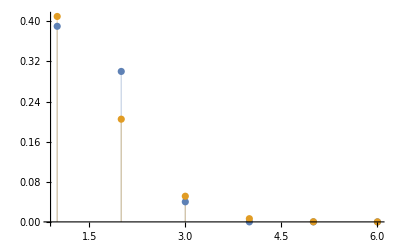

```mathematica
ListPlot[{Transpose[{Range[6],PDF[ld,Range[6]]}],Table[{k,PDF[BinomialDistribution[5,0.2],k]},{k,1,6}]},Filling->Axis,PlotRange->All]
```

### Continuous random variable

Consider the snow accumulation in Buffalo:

```mathematica
buffaloSnow=ExampleData[{"Statistics","BuffaloSnow"},"DataElements"];
```

```mathematica
buffaloSnow
```

{126.4,82.4,78.1,51.1,90.9,76.2,104.5,87.4,110.5,25,69.3,53.5,39.8,63.6,46.7,72.9,79.7,83.6,80.7,60.3,79,74.4,49.6,54.7,71.8,49.1,103.9,51.6,82.4,83.6,77.8,79.3,89.6,85.5,58,120.7,110.5,65.4,39.9,40.1,88.7,71.4,83,55.9,89.9,84.8,105.2,113.7,124.7,114.5,115.6,102.4,101.4,89.8,71.5,70.9,98.3,55.5,66.1,78.4,120.5,97,110}

```mathematica
ld=LearnDistribution[buffaloSnow]
```

LearnedDistribution[…]

The trained distribution can be used to provide a possible snow accumulation in a random year in the future:

```mathematica
RandomVariate[ld]
```

100.752

The original dataset contains 63 data points (corresponding to 63 years):

```mathematica
Length[buffaloSnow]
```

63

The trained distribution can be used to generate data for many more years:

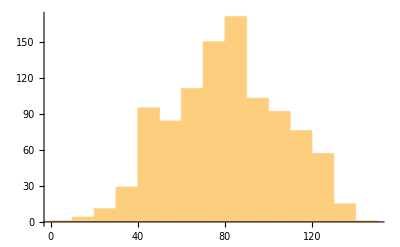

```mathematica
Histogram[RandomVariate[ld,1000]]
```

Trying to compare the histogram for random variates of the learnt distribution ld and the histogram for the original data buffaloSnow

Simply using Histogram: It gives a histogram for frequencies in each bin and it is difficult to compare since there are 1000 random variates from ld and only 63 data in buffaloSnow.

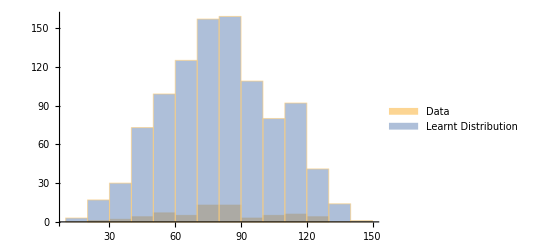

```mathematica
Histogram[{buffaloSnow,RandomVariate[ld,1000]},ChartLegends->{"Data","Learnt Distribution"}]
```

Plotting histograms for the probability to fall in each bin (i.e. probability instead of frequency). This gives a better comparison between the two histograms.

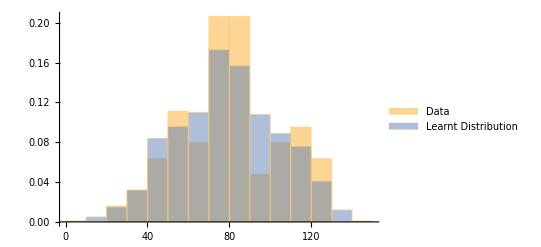

```mathematica
Histogram[{buffaloSnow,RandomVariate[ld,1000]},Automatic,"Probability",ChartLegends->{"Data","Learnt Distribution"}]
```

One can use the extended dataset to find a suitable distribution to describe the data:

```mathematica
estimated𝒟2=FindDistribution[RandomVariate[ld,1000],3]
```

{WeibullDistribution[3.46529,89.3144],NormalDistribution[80.2306,25.9814],MixtureDistribution[{0.463908,0.536092},{NormalDistribution[61.5228,19.4336],NormalDistribution[96.4194,19.1682]}]}

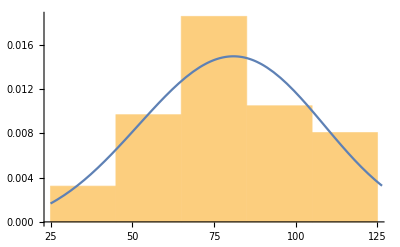

```mathematica
Show[{Histogram[buffaloSnow,{Min[buffaloSnow],Max[buffaloSnow],20},"PDF"],Plot[PDF[estimated𝒟2[[1]],x],{x,Min[buffaloSnow],Max[buffaloSnow]}]}]
```

### Task for you

Extend the data of weights of chickens you studied above to find a suitable distribution of the weight using more data than in the original dataset

### Nominal dataset

A distribution can be also trained on a nominal dataset:

```mathematica
ld=LearnDistribution[{"A","A","B","B","B"}]
```

LearnedDistribution[…]

A random variate

```mathematica
RandomVariate[ld]
```

B

As expected, “B” appears more often than “A” if enough random variates are drawn:

```mathematica
Tally[RandomVariate[ld,1000]]
```

{{B,555},{A,445}}

```mathematica
PDF[ld,{"A","B"}]
```

{0.428571,0.571429}

```mathematica
N[2/5]
```

0.4

```mathematica
N[3/5]
```

0.6